# Bell Violation

## CHSH Inequality - Noon State & Two-Mode Squeezed State

Valerio Paper

Emlyn Graham

Department of Quantum Science

19/08/2018

```mathematica
SetOptions[Plot,Frame->True,Axes->False,LabelStyle->{FontFamily->"Arial",FontSize->10}];SetOptions[ContourPlot,Frame->True,Axes->False,LabelStyle->{FontFamily->"Arial",FontSize->10}];
```

## Noon State

#### Eigenfunctions of Quantum Harmonic Oscillator

We define the eigenfunctions as follows:

```mathematica
ϕ[n_,x_]=FullSimplify[((π^(1/4)*Sqrt[n!*2^n])^(-1))*HermiteH[n,x]*Exp[-(x^2)/2]]
```

(ⅇ^(-x^2/2) HermiteH[n,x])/(π^(1/4) √(2^n n!))

The specific eigenfunctions used in this case are as follows:

```mathematica
ϕ[0,x]
```

(ⅇ^(-x^2/2))/π^(1/4)

```mathematica
ϕ[1,x]
```

(√2 ⅇ^(-x^2/2) x)/π^(1/4)

```mathematica
ϕ[2,x]
```

(ⅇ^(-x^2/2) (-2+4 x^2))/(2 √2 π^(1/4))

where we can see that for 0 and 2 they match those stated in the paper. This can be further checked by plotting the density functions of both of these as seen in the paper.

(2^(-Re[n]) ⅇ^(-Re[x^2]) Abs[HermiteH[n,x]]^2)/(√π Abs[n!])

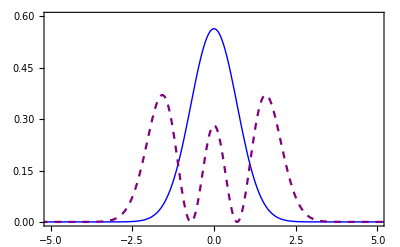

```mathematica
Densityϕ[n_,x_]=Abs[ϕ[n,x]]^2
DensityPlotϕ[n_,colour_,style_] := Plot[Densityϕ[n,x],{x,-10,10},Frame->True,PlotRange->{{-5,5},{0,0.6}},AxesOrigin->{-5,5},PlotStyle->{style,colour}]
Show[DensityPlotϕ[0,Blue,Thin],DensityPlotϕ[2,Purple,Dashed]]
```

#### Probabilities with loss factor

We define the integrals of the ϕ functions for the disjoint regions [-z,z] and ℝ\[-z,z], checking as we go:

```mathematica
IntegralDensityϕ[n_,region_,z_]=Piecewise[{{Integrate[Densityϕ[n,x],{x,-z,z},Assumptions->z∈Reals&&n∈Integers&&n>-1],region==1},{1-Integrate[Densityϕ[n,x],{x,-z,z},Assumptions->z∈Reals&&n∈Integers&&n>-1],region==-1}}];
FullSimplify[IntegralDensityϕ[0,1,z]+IntegralDensityϕ[0,-1,z]]==1
```

True

```mathematica
FullSimplify[IntegralDensityϕ[2,1,z]+IntegralDensityϕ[2,-1,z]]==1
```

True

```mathematica
IntegralProductϕ02[region_,z_]=Piecewise[{{Integrate[ϕ[0,x]*ϕ[2,x],{x,-z,z},Assumptions->z∈Reals],region==1},{Integrate[ϕ[0,x]*ϕ[2,x],{x,-Infinity,-z},Assumptions->z∈Reals]+Integrate[ϕ[0,x]*ϕ[2,x],{x,z,Infinity},Assumptions->z∈Reals],region==-1}}];
FullSimplify[IntegralProductϕ02[1,z]+IntegralProductϕ02[-1,z]]==0
```

True

Now we start defining the probability functions of each measurement combination:

```mathematica
PNN[t_,a_,b_]=Piecewise[{{0,a==1&&b==1},{((1-t)^2),a==-1&&b==-1},{((t^2)/2) + (t*(1-t)),a==1&&b==-1},{((t^2)/2) + (t*(1-t)),a==-1&&b==1}}];
PNN[1,1,1]+PNN[1,1,-1]+PNN[1,-1,1]+PNN[1,-1,-1]==1
```

True

```mathematica
PNN[1,1,1]-PNN[1,1,-1]-PNN[1,-1,1]+PNN[1,-1,-1]==-1
```

True

```mathematica
PNX[t_,a_,b_,z_]=Piecewise[{{((t^2/2)+t*(1-t))*IntegralDensityϕ[0,1,z],a==1&&b==1},{(t^2/2)*IntegralDensityϕ[2,-1,z]+(t*(1-t))*IntegralDensityϕ[1,-1,z]+((1-t)^2)*IntegralDensityϕ[0,-1,z],a==-1&&b==-1},{((t^2/2)+t*(1-t))*IntegralDensityϕ[0,-1,z],a==1&&b==-1},{(t^2/2)*IntegralDensityϕ[2,1,z]+(t*(1-t))*IntegralDensityϕ[1,1,z]+((1-t)^2)*IntegralDensityϕ[0,1,z],a==-1&&b==1}}];
FullSimplify[PNX[1,1,1,z]+PNX[1,1,-1,z]+PNX[1,-1,1,z]+PNX[1,-1,-1,z]]==1
```

True

```mathematica
PXX[t_,a_,b_,z_]=Piecewise[{{(t^2/2)*(2*IntegralDensityϕ[0,1,z]*IntegralDensityϕ[2,1,z]+2*(IntegralProductϕ02[1,z])^2) + t*(1-t)*(IntegralDensityϕ[1,1,z]*IntegralDensityϕ[0,1,z])+((1-t)^2)*(IntegralDensityϕ[0,1,z])^2,a==1&&b==1},{(t^2/2)*(2*IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[2,-1,z]+2*(IntegralProductϕ02[-1,z])^2) + t*(1-t)*(IntegralDensityϕ[1,-1,z]*IntegralDensityϕ[0,-1,z])+((1-t)^2)*(IntegralDensityϕ[0,-1,z])^2,a==-1&&b==-1},{(t^2/2)*(IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[2,1,z]+IntegralDensityϕ[2,-1,z]*IntegralDensityϕ[0,1,z]+2*(IntegralProductϕ02[1,z]*IntegralProductϕ02[-1,z]))+t*(1-t)*(IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[1,1,z]+IntegralDensityϕ[1,-1,z]*IntegralDensityϕ[0,1,z])+((1-t)^2)*(IntegralDensityϕ[0,1,z]*IntegralDensityϕ[0,-1,z]),a==1&&b==-1},{(t^2/2)*(IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[2,1,z]+IntegralDensityϕ[2,-1,z]*IntegralDensityϕ[0,1,z]+2*(IntegralProductϕ02[1,z]*IntegralProductϕ02[-1,z]))+t*(1-t)*(IntegralDensityϕ[0,-1,z]*IntegralDensityϕ[1,1,z]+IntegralDensityϕ[1,-1,z]*IntegralDensityϕ[0,1,z])+((1-t)^2)*(IntegralDensityϕ[0,1,z]*IntegralDensityϕ[0,-1,z]),a==-1&&b==1}}];
FullSimplify[PXX[1,1,1,1]+PXX[1,1,-1,1]+PXX[1,-1,1,1]+PXX[1,-1,-1,1]]==1
```

True

#### Expectation values

Now we start defining the expectation value of each measurement combination, and try plotting:

```mathematica
ENN[t_]=PNN[t,1,1]+PNN[t,-1,-1]-PNN[t,1,-1]-PNN[t,-1,1];
ENX[t_,z_]=PNX[t,1,1,z]+PNX[t,-1,-1,z]-PNX[t,1,-1,z]-PNX[t,-1,1,z];
EXN[t_,z_]=ENX[t,z];
EXX[t_,z_]=PXX[t,1,1,z]+PXX[t,-1,-1,z]-PXX[t,1,-1,z]-PXX[t,-1,1,z];
S[t_,z_]=EXX[t,z]+2*ENX[t,z]-ENN[t];
FullSimplify[S[1,0]]==2
```

True

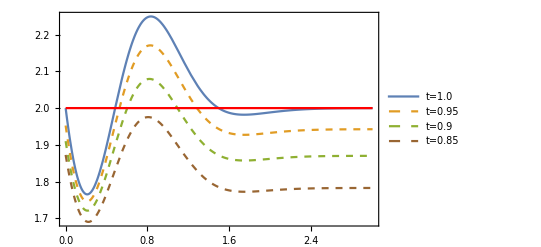

```mathematica
NoonTZPlot = Plot[{S[1.0,z],S[0.95,z],S[0.9,z],S[0.85,z],2.},{z,0.,3.},PlotLegends->LineLegend[{"t=1.0","t=0.95","t=0.9","t=0.85"}],PlotStyle->{Thick,Dashed,Dashed,{Dashed,Brown},{Thin,Red}}]
```

```mathematica
Export["C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/NoonTZPlot.eps",NoonTZPlot]
```

C:/Users/emlyn/Google Drive/Undergrad 5th year/Semester 2/Quantum Computing/NoonTZPlot.eps

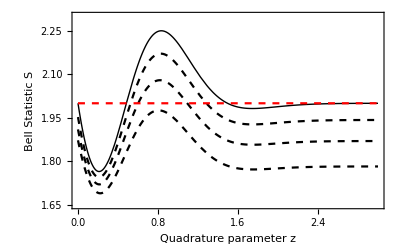

```mathematica
SPlot[t_,colour_,style_] := Plot[S[t,z],{z,0,3},Frame->True,PlotRange->{{0,3},{1.65,2.3}},AxesOrigin->{0,3},PlotStyle->{style,colour}, FrameLabel->{"Quadrature parameter z","Bell Statistic S"}]
Show[SPlot[1,Black,Thin],SPlot[0.95,Black,Dashed],SPlot[0.90,Black,Dashed],SPlot[0.85,Black,Dashed],Plot[2,{z,0,3},Frame->True,PlotRange->{{0,3},{1.7,2.3}},AxesOrigin->{0,3},PlotStyle->{Dashed,Red}]]
```

```mathematica
NMaximize[{S[1.,z],{z>0}},z]
```

{2.24955,{z→0.833283}}

{{0.8601,1.99743},{0.8602,1.99765},{0.8603,1.99786},{0.8604,1.99808},{0.8605,1.99829},{0.8606,1.99851},{0.8607,1.99872},{0.8608,1.99894},{0.8609,1.99915},{0.861,1.99937},{0.8611,1.99958},{0.8612,1.9998},{0.8613,2.00001},{0.8614,2.00023},{0.8615,2.00044},{0.8616,2.00066},{0.8617,2.00087},{0.8618,2.00108},{0.8619,2.0013},{0.862,2.00151},{0.8621,2.00173},{0.8622,2.00194},{0.8623,2.00216},{0.8624,2.00237},{0.8625,2.00258},{0.8626,2.0028},{0.8627,2.00301},{0.8628,2.00323},{0.8629,2.00344},{0.863,2.00365}}

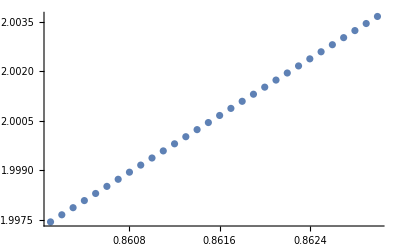

```mathematica
Maxima = Table[{0.86+n*0.0001,FindMaxValue[{S[0.86+n*0.0001,z],0≤ z≤ 10},z]},{n, 30}]
ListPlot[Maxima]
```

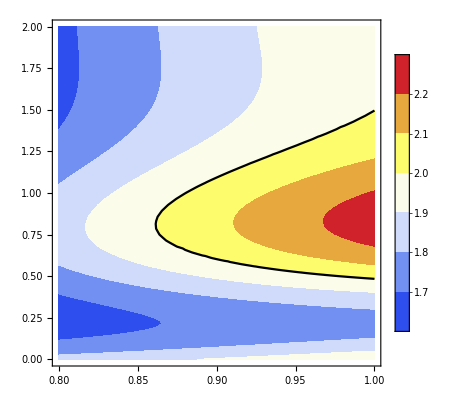

```mathematica
Show[ContourPlot[S[t,z], {t,0.8,1.0},{z,0.,2.}, PlotRange->All, PlotLegends->Automatic,ContourStyle->None,ColorFunction->"TemperatureMap"],ContourPlot[S[t,z]==2., {t,0.8,1.0},{z,0.,2.}, PlotRange->All, PlotLegends->Automatic,ContourStyle->Black]]
```

## Squeezed State - Orthogonal Quadrature

#### Eigenfunctions of Quantum Harmonic Oscillator

We define the useful eigenfunctions and their integrals as follows, as well as setting a λ value:

```mathematica
λ := 0.83;
SumLimit := 20
SumLimit
```

20

```mathematica
ϕ[n_,x_]=FullSimplify[((π^(1/4)*Sqrt[n!*2^n])^(-1))*HermiteH[n,x]*Exp[-(x^2)/2]]
```

(ⅇ^(-x^2/2) HermiteH[n,x])/(π^(1/4) √(2^n n!))

```mathematica
Densityϕ[n_,x_]:=RealAbs[ϕ[n,x]^2];
HermiteSum[x_,y_] := RealAbs[(Sum[(λ^(n))*(ϕ[n,x]*ϕ[n,y]),{n,0,SumLimit}])]*RealAbs[(Sum[(λ^(m))*(ϕ[m,x]*ϕ[m,y]),{m,0,SumLimit}])];
IntegralDensityϕ[n_,region_,z_]:=Piecewise[{{Integrate[Densityϕ[n,x],{x,-z,z},Assumptions->z∈Reals&&n∈Integers&&n>-1],region==1},{1-Integrate[Densityϕ[n,x],{x,-z,z},Assumptions->z∈Reals&&n∈Integers&&n>-1],region==-1}}];
FullSimplify[IntegralDensityϕ[1,1,z]+IntegralDensityϕ[1,-1,z]]
```

1

#### Probabilities and expectation values

```mathematica
ENN = RealAbs[Sum[(1-λ^2)*λ^(2*n),{n,0,Infinity}]]
```

1.

```mathematica
PNX[a_,b_,z_]:= Piecewise[
{{(1-λ^2)*NIntegrate[RealAbs[Sum[(λ^n)^2*ϕ[n,x]^2,{n,1,SumLimit}]],{x,-z,z},AccuracyGoal->6],a==1&&b==1},
{(1-λ^2)*(IntegralDensityϕ[0,-1,z]),a==-1&&b==-1},
{(1-λ^2)*IntegralDensityϕ[0,1,z],a==-1&&b==1},
{(1-λ^2)*NIntegrate[RealAbs[Sum[(λ^n)^2*ϕ[n,x]^2,{n,1,SumLimit}]],{x,-Infinity,-z},AccuracyGoal->6]+(1-λ^2)*NIntegrate[RealAbs[Sum[(λ^n)^2*ϕ[n,x]^2,{n,1,SumLimit}]],{x,z,Infinity},AccuracyGoal->6],a==1&&b==-1}}
]
FullSimplify[PNX[1,1,1]+PNX[-1,-1,1]+PNX[1,-1,1]+PNX[-1,1,1]]
ENX[z_]:=PNX[1,1,z]+PNX[-1,-1,z]-PNX[1,-1,z]-PNX[-1,1,z];
```

0.999601

```mathematica
PXpositive[z_] := (1-λ^2)*NIntegrate[HermiteSum[x,y],{x,-z,z},{y,-Infinity,Infinity}]
PXnegative[z_]:=(1-λ^2)*(NIntegrate[HermiteSum[x,y],{x,-Infinity,-z},{y,-Infinity,Infinity}]+NIntegrate[HermiteSum[x,y],{x,z,Infinity},{y,-Infinity,Infinity}])
PXpositive[1]+PXnegative[1]
```

0.999601

```mathematica
PXX[a_,b_,z_]:=Piecewise[{{PXpositive[z]^2,a==1&&b==1},{PXnegative[z]^2,a==-1&&b==-1},{PXpositive[z]*PXnegative[z],a==1&&b==-1},{PXpositive[z]*PXnegative[z],a==-1&&b==1}}];
FullSimplify[PXX[1,1,1]+PXX[-1,-1,1]+PXX[1,-1,1]+PXX[-1,1,1]]
EXX[z_]:=PXX[1,1,z]+PXX[-1,-1,z]-PXX[1,-1,z]-PXX[-1,1,z];
```

0.999202

```mathematica
S[z_]:=RealAbs[FullSimplify[EXX[z]+2*ENX[z]-1]];
S[0.86]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

2.05198

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

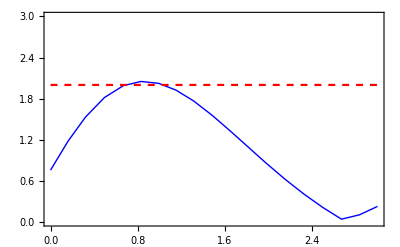

```mathematica
Show[Plot[S[z],{z,0,3},Frame->True,PlotRange->{{0,3},{0,3}},AxesOrigin->{0,3},PlotStyle->{Thin,Blue}, PlotPoints->10, MaxRecursion->1],Plot[2,{z,0,3},Frame->True,PlotRange->{{0,3},{0,3}},AxesOrigin->{0,3},PlotStyle->{Dashed,Red}]]
```